## Initialization

Load packages

```mathematica
$HistoryLength=1;
(*If package is installed to a non standard dir add it to path just in case*)
With[{pfn=ExpandFileName@FileNameJoin[{NotebookDirectory[],"..",".."}]},
If[!MemberQ[$Path,pfn], PrependTo[$Path,pfn]];
];
Needs["Developer`"]
Needs["DiffusiveDynamics`"]
(*Load the data on paralle Kernels*)
CloseKernels[];
With[{path=$Path},
ParallelEvaluate[
$Path=path;(*add to the path of parallel Kernels*)
$HistoryLength=1;
Needs["Developer`"];
Needs["DiffusiveDynamics`"];
]];
$VerbosePrint=True;

R[α_]:={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};
DDD[Dx_,Dy_]:={{1/Dx^2,0},{0,1/Dy^2}};
D2DMat[Dx_,Dy_,α_]:=N[R[α °].DDD[Dx,Dy].Transpose[R[α °]]];
```

Reloaded DiffusiveDynamics`!

Reloaded DiffusiveDynamics`!

Reloaded DiffusiveDynamics`!

«3 more identical outputs»

Define diffusion parameters

```mathematica
STEPS=2000000;
STEP=1;
CELLRANGE={1000.,500.};
ModI[x_,halfwidth_]:=Mod[x+halfwidth,2*halfwidth]-halfwidth;
ClearAll[DIFFX,DIFFY,DIFFA];
DIFFX=Compile[{x,y},
5Sin[x/ CELLRANGE[[1]] π] +10];
DIFFY=Compile[{x,y},
5Sin[y/ CELLRANGE[[2]] π] +10];
DIFFA=Compile[{x,y},
(((x/2)/CELLRANGE[[1]])^2+((y/2)/ CELLRANGE[[2]])^2)*180];


TENSOR[x_,y_]:=D2DMat[DIFFX[x,y],DIFFY[x,y],DIFFA[x,y]];
ClearAll[ENERGY]; (*energija v enotah kT*)
ENERGY=Compile[{x,y},1];
KT=1.;
CELL$plots=DiffusionParameters2DPlots[DIFFX,DIFFY,DIFFA,ENERGY,CELLRANGE]
StringForm["STEPS `1`; STEP `2`; KT `3`",STEPS,STEP,KT];
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Generate Data

{0.73104,Null}

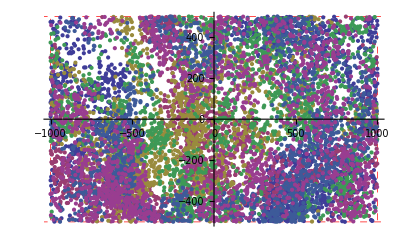

```mathematica
$VerbosePrint = True;
$VerboseLevel = 3;
AbsoluteTiming[
 rw = ParallelGenerateDiffusionTrajectory2D[STEPS=800000 , DIFFX, DIFFY, DIFFA, ENERGY, KT, STEP, {-CELLRANGE, CELLRANGE}, Verbose -> False,"VerboseLevel"->3, "InitialPositions" -> Automatic, "ProcessCount" -> 6];
 ]


w = {250, 125}*1;(*width of bin*)
w0 = {0, 0}; (*lower left point of bin*)
ListPlot[rw[[All, ;; ;; Ceiling[STEPS/10000], {2, 3}]], PlotRange -> Transpose@{-CELLRANGE, CELLRANGE}, GridLines -> Transpose@{-CELLRANGE, CELLRANGE}, GridLinesStyle -> Directive[Red, Thick, Dashed],
 Epilog -> {Opacity[0], EdgeForm[{Red, Thick}], Rectangle[w0 - w/2, w0 + w/2]}]
```

## Analyze diffusion

```mathematica
w=CELLRANGE/4;
binSpec=Transpose[{-CELLRANGE,CELLRANGE,w}];
AbsoluteTiming[diffs=GetDiffusionInBins[rw,STEP,binSpec,"CellRange"->{-CELLRANGE,CELLRANGE},Verbose->False,"Strides"->{1,5,7,10,20,30,40,50,60,70,80,90,100},"PadSteps"->True,Parallel->True,"ReturnStepsHistogram"->True,"WarnIfEmpty"->False];]
```

{41.27736,Null}

```mathematica
filename="diff.mx.gz";
AbsoluteTiming@Export[filename,diffs,"CompressionLevel"->.1]
```

{4.15324,diff.mx.gz}

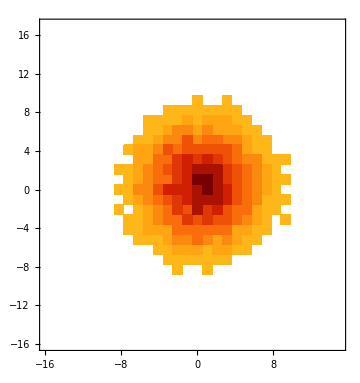
{{Dx→8.11555,Dy→7.99329,«10»,StepsInBin→17995,StepsHistogram→-Graphics-},«11»,{«1»}}

```mathematica
AbsoluteTiming[diffs=Import[filename]];
Short@First@diffs
```

```mathematica
bins=ToPackedArray[ GetValues[{{"x","y"},{"xWidth","yWidth"}},diffs[[All,1]]]];
fittedG=DrawDiffusionTensorRepresentations[diffs[[All,1]],Scale->3,"OutlineStyle"->{Black,Thick,Opacity@.5},"FillStyle"->{Black,Opacity@.5}];
actualG=DrawDiffusionTensorRepresentations[
GetDiffusionInfoFromParameters[binSpec,DIFFX,DIFFY,DIFFA],Scale->3,"OutlineStyle"->{Red,Thick,Opacity@.5},"FillStyle"->{Red,Opacity@.5}];
Show[actualG,fittedG,ImageSize->Large]
```

```mathematica
Compile
```

```mathematica
FrameLabel
```

```mathematica
ViewDiffsWithStridePlots[diffs,"Difuzija",SaveDefinitions->False,Verbose->False]
```

```mathematica
Short[bins=GetValues[{{"x","y"},{"xWidth","yWidth"}},diffs[[All,1]]]]
cellRange=GetCellRangeFromBins@bins
DrawDiffusionTensorRepresentations[diffs[[All,1]],"Scale"->4,"CellRange"->cellRange]
```

```mathematica
si=8;
DrawDiffusionTensorRepresentations[diffs[[All,si]],"Scale"->4,Verbose->True,"MarkNonNormal"->True]
```

```mathematica
l1={True,False,False,True};
l2={1,2,3,4};
Pick[l2,l1]
```

```mathematica
ImagePadding
```

## misc

```mathematica
(*For easier storage in Git*)
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False];FrontEndTokenExecute["DeleteGeneratedCells"];
(*Auto delete output on close*)
```

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndTokenExecute["DeleteGeneratedCells"]}];
```